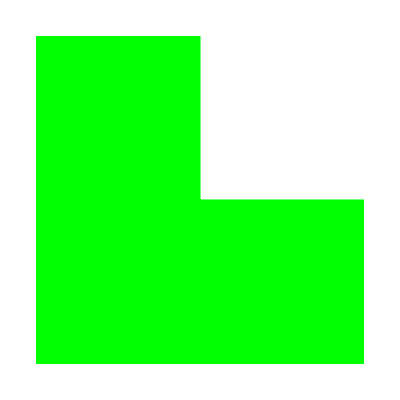

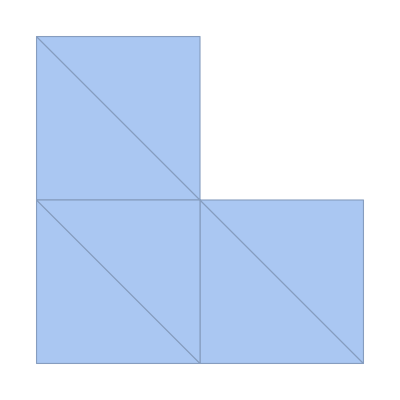

1

Part::partw: Part 2 of PolygonCoordinates[Polygon[{{0,0},{1,0},{0,1}}]] does not exist.

Part::partw: Part 3 of PolygonCoordinates[Polygon[{{0,0},{1,0},{0,1}}]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

LinearSolve::matrix: Argument {Polygon[{{0,0},{1,0},{0,1}},1],PolygonCoordinates[Polygon[{{0,0},{1,0},{0,1}}]]⟦2,1⟧,PolygonCoordinates[Polygon[{{0,0},{1,0},{0,1}}]]⟦3,1⟧} at position 1 is not a non-empty rectangular matrix.

General::stop: Further output of LinearSolve::matrix will be suppressed during this calculation.

-Graphics3D-

```mathematica
P={
{0,0},
{1,0},
{2,0},
{0,1},
{1,1},
{2,1},
{0,2},
{1,2}
};
T={
{1,2,4},
{2,5,4},
{2,3,5},
{3,6,5},
{4,5,7},
{5,8,7}
};
constructElements[nodes_,nodeIndexArr_]:=Polygon[Table[nodes⟦#⟦k⟧⟧,{k,1,Length[#]}]]&/@nodeIndexArr
triangleTable =constructElements[P,T];
Graphics[{EdgeForm[Directive[Dashed]],Green,triangleTable}]
meshReg=MeshRegion[P,Polygon/@T]
testpoint[poly_,pt_]:=
Round[
(Total@Mod[(#-RotateRight[#])&@(If[pt-#≠{0,0},ArcTan@@(pt-#),1]&/@poly),2 Pi,-Pi]/2/Pi)]≠0
inRegion[regions_,coordinates_]:=Module[{ind=1,len=Length[regions]},
While[!(coordinates∈regions⟦ind⟧),
++ind;
If[ind>len,ind=0;Break[]];
];
ind
]
inRegion2[nodes_,nodeIndexArr_,coordinates_]:=Module[{ind=1,len=Length[nodeIndexArr]},
While[!testpoint[nodes⟦#⟧& /@ nodeIndexArr⟦ind⟧,coordinates],
++ind;
If[ind>len,ind=0;Break[]];
];
ind
]
inRegion[triangleTable, {1,0}]
(*inRegion[meshReg, {1,0}]*)
hatFunctions[k_,nodes_?ListQ,elements_?ListQ,coordinates_]:=Module[{el,elIndex,dims=Length[nodes⟦1⟧]},
regionCond[testPoly_]:=RegionMember[testPoly,coordinates];
 (*If not found, return 0*)
el=SelectFirst[elements,regionCond];
If[MissingQ[el], Return[0]];

(*If it is not part of the region of elements, return 0*)
(*If[!MemberQ[PolygonCoordinates[el],nodes⟦k⟧], Return[0]];*)
(*If[elIndex==0, Return[0]];*)


(*nodesForElement = nodeIndexArr⟦elIndex⟧;*)
(*Take which index in vector equation must have non-zero in RHS*)
(*indexInPolygon=FirstPosition[nodesForElement,k];*)
nodeCoords = PolygonCoordinates[el];
indexInPolygon=FirstPosition[nodeCoords,nodes⟦k⟧];
If[MissingQ[indexInPolygon], Return[0]];

rhs=Table[0,dims+1];
rhs⟦indexInPolygon⟧=1;
lhs=Table[Append[nodeCoords⟦j⟧,1],{j,1,dims+1}];
coeffs = LinearSolve[lhs,rhs];
Return[Sum[coeffs⟦j⟧coordinates⟦j⟧,{j,1,dims}]+coeffs⟦dims+1⟧]
]

(*Plot3D[hatFunctions[5,P,T,triangleTable,{x,y}],{x,y} ∈ meshReg,PlotPoints->10]*)

phi[coordinates_?ListQ]:=coordinates⟦1⟧^2+coordinates⟦2⟧^2
nodeInterpolate[nodes_?ListQ,elements_?ListQ,f_,coordinates_]:=Sum[f[nodes⟦k⟧] hatFunctions[k,nodes,elements,coordinates],{k,1,Length[nodes]}]
Plot3D[nodeInterpolate[P,triangleTable,phi,{x,y}],{x,y} ∈ meshReg,PlotPoints->10]
```

```mathematica
(*triangleTable = Function[element,
Triangle[Table[P⟦element⟦k⟧⟧,{k,1,Length[element]}]]
]/@T;
Position[triangleTable, RegionMember[_,{1,1}]]
Position[triangleTable, {0.5,0.5}∈_]*)
```

```mathematica
Plot3D[phi[{x,y}],{x,y} ∈ meshReg,PlotPoints->10]
```

-Graphics3D-

```mathematica
hatFunctions[k_,nodes_?ListQ,nodeIndexArr_?ListQ,elements_?ListQ,coordinates_]:=Module[{elIndex=inRegion2[nodes, nodeIndexArr,coordinates],dims=Length[nodes⟦1⟧]},
(*If it is not part of the region of elements, return 0*)
If[elIndex==0, Return[0]];
nodesForElement = nodeIndexArr⟦elIndex⟧;
(*Take which index in vector equation must have non-zero in RHS*)
indexInPolygon=FirstPosition[nodesForElement,k];
If[MissingQ[indexInPolygon], Return[0]];
rhs=Table[0,dims+1];
rhs⟦indexInPolygon⟧=1;
lhs=Table[Append[nodes⟦nodesForElement⟦j⟧⟧,1],{j,1,dims+1}];
coeffs = LinearSolve[lhs,rhs];
Return[Sum[coeffs⟦j⟧coordinates⟦j⟧,{j,1,dims}]+coeffs⟦dims+1⟧]
]
```

```mathematica
P={
{0,0},
{1,0},
{2,0},
{0,1},
{1,1},
{2,1},
{0,2},
{1,2}
};
T={
{1,2,4},
{2,5,4},
{2,3,5},
{3,6,5},
{4,5,7},
{5,8,7}
};
AssembleMatrix[nodes_,nodeIndexArr_,localMatrix_]:=(
globalMatrix = Table[Table[0,Length[nodes]],Length[nodes]];
localRows = Length[localMatrix];
localCols = Length[localMatrix⟦1⟧];
For[k=1,k≤Length[nodeIndexArr],k++,
element = nodeIndexArr⟦k⟧;
For[i=1,i≤localRows,i++,
For[j=1,j≤localCols,j++,
globalMatrix⟦element⟦i⟧,element⟦j⟧⟧+=localMatrix⟦i, j⟧;
];
];
];
globalMatrix
)
phi[coordinates_?ListQ]:=coordinates⟦1⟧^2+coordinates⟦2⟧^2
Subscript[ψ, 0][{ξ_,η_}]:=1-ξ-η
Subscript[ψ, 1][{ξ_,η_}]:=ξ
Subscript[ψ, 2][{ξ_,η_}]:=η
(*localLoadVector[f_,jacobian_,elNodes_,quadPoints_,quadWeights_]:=Det[jacobian]{
0.5 f[jacobian*{0.5,0}+elNodes⟦0⟧] ,
0.5 f[jacobian*{0.5,0.5}+elNodes⟦0⟧]
}*)
loadVector[f_,jacobian_,elNodes_]:=(
(*Print[1/6 Det[jacobian]Table[
Subscript[ψ, s][{0.5,0}]f[jacobian.{0.5,0}+elNodes⟦1⟧]+
Subscript[ψ, s][{0.5,0.5}]f[jacobian.{0.5,0.5}+elNodes⟦1⟧]+
Subscript[ψ, s][{0,0.5}]f[jacobian.{0,0.5}+elNodes⟦1⟧],{s,0,2}]];*)
1/6 Det[jacobian]Table[
Subscript[ψ, s][{0.5,0}]f[jacobian.{0.5,0}+elNodes⟦1⟧]+
Subscript[ψ, s][{0.5,0.5}]f[jacobian.{0.5,0.5}+elNodes⟦1⟧]+
Subscript[ψ, s][{0,0.5}]f[jacobian.{0,0.5}+elNodes⟦1⟧],{s,0,2}])
(*loadVector[phi,{{1,0},{0,1}},{{0,0},{1,0},{0,1}}]*)
(*1/6 Det[{{1,0},{0,1}}]Table[
Subscript[ψ, s][{0.5,0}]phi[{{1,0},{0,1}}.{0.5,0}+{{0,0},{1,0},{0,1}}⟦1⟧]+
Subscript[ψ, s][{0.5,0.5}]phi[{{1,0},{0,1}}.{0.5,0.5}+{{0,0},{1,0},{0,1}}⟦1⟧]+
Subscript[ψ, s][{0,0.5}]phi[{{1,0},{0,1}}.{0,0.5}+{{0,0},{1,0},{0,1}}⟦1⟧],{s,0,2}]*)

AssembleLoadVector[nodes_,nodeIndexArr_,loadVector_,f_]:=(
globalLoadVector = Table[0,Length[nodes]];
loadRows = Length[nodeIndexArr⟦1⟧];
For[kk=1,kk≤Length[nodeIndexArr],kk++,
element = nodeIndexArr⟦kk⟧;
{{Subscript[x, k],Subscript[y, k]},{Subscript[x, l],Subscript[y, l]},{Subscript[x, m],Subscript[y, m]}}=nodes⟦element⟧;
(*jacobian = {{Subscript[x, l]-Subscript[x, k],Subscript[y, l]-Subscript[y, k]},{Subscript[x, m]-Subscript[x, k],Subscript[y, m]-Subscript[y, k]}};*)
jacobian = {{Subscript[x, l]-Subscript[x, k],Subscript[x, m]-Subscript[x, k]},{Subscript[y, l]-Subscript[y, k],Subscript[y, m]-Subscript[y, k]}};
localLoadVector=loadVector[f,jacobian,nodes⟦element⟧];
For[i=1,i≤loadRows,i++,
globalLoadVector⟦element⟦i⟧⟧+=localLoadVector⟦i⟧;
];
];
globalLoadVector
)
locMatrix = 1/24 {{2,1,1},{1,2,1},{1,1,2}};
globalMat = AssembleMatrix[P,T,locMatrix];
globalLoad =AssembleLoadVector[P,T,loadVector,phi];
sol = LinearSolve[globalMat,globalLoad];
L2Projection[nodes_?ListQ,nodeIndexArr_?ListQ,elements_?ListQ,f_,coordinates_,sol_]:=sol.Table[ hatFunctions[k,nodes,nodeIndexArr,elements,coordinates],{k,1,Length[nodes]}]

Plot3D[{phi[{x,y}],L2Projection[P,T,triangleTable,phi,{x,y},sol]},{x,y} ∈ meshReg,PlotPoints->10]
```

(1/12 | 1/24 | 0 | 1/24 | 0 | 0 | 0 | 0
1/24 | 1/4 | 1/24 | 1/12 | 1/12 | 0 | 0 | 0
0 | 1/24 | 1/6 | 0 | 1/12 | 1/24 | 0 | 0
1/24 | 1/12 | 0 | 1/4 | 1/12 | 0 | 1/24 | 0
0 | 1/12 | 1/12 | 1/12 | 5/12 | 1/24 | 1/12 | 1/24
0 | 0 | 1/24 | 0 | 1/24 | 1/12 | 0 | 0
0 | 0 | 0 | 1/24 | 1/12 | 0 | 1/6 | 1/24
0 | 0 | 0 | 0 | 1/24 | 0 | 1/24 | 1/12)

{0.0416667,0.5,0.958333,0.5,1.79167,0.625,0.958333,0.625}

{-0.170732,0.670732,3.53659,0.670732,1.63415,4.91463,3.53659,4.91463}

-Graphics3D-

```mathematica
vars=Array[Subscript[x, #]&,2];
linearStretch = {{Subscript[a, 1],Subscript[b, 1]},{Subscript[a, 2],Subscript[b, 2]}} ;
translation =  {Subscript[c, 1],Subscript[c, 2]};
f=linearStretch. vars + translation
MatrixForm[D[f,{vars}]]
```

{c_1+a_1 x_1+b_1 x_2,c_2+a_2 x_1+b_2 x_2}

(a_1 | b_1
a_2 | b_2)